```mathematica
x0={-1,1};
F[x1_,x2_]=100(x2-x1^2)^2+(1-x1)^2;
```

```mathematica
Plot3D[F[x1,x2],{x1,-2,2},{x2,-2,2}]
```

-Graphics3D-

```mathematica
G1 = ContourPlot[F[x1,x2],{x1,-3,3},{x2,-3,3}];
```

```mathematica
x00={x0,{-1.0005,0.9995}};
```

```mathematica
MatrixForm[x00]
```

(-1 | 1
-1.0005 | 0.9995)

```mathematica
GrVToch[x1_,x2_]=Grad[F[x1,x2],{x1,x2}];
```

```mathematica
tabl={{"Итерация","u_1","u_2","x_1","x_2","F[x̄]","||∇F(x̄)||"},{"Начало","-","-",x0[[1]],x0[[2]],F[x0[[1]],x0[[2]]],Norm[GrVToch[x0[[1]],x0[[2]]],2]}};
Srav = {{"Метод","Время выполнения метода","Количество итераций"}};
```

```mathematica
Φ1[a_]=F[x00[[1,1]]-a*GrVToch[x00[[1,1]],x00[[1,2]]][[1]],x00[[1,2]]-a*GrVToch[x00[[1,1]],x00[[1,2]]][[2]]];
```

```mathematica
Φ2[a_]=F[x00[[2,1]]-a*GrVToch[x00[[2,1]],x00[[2,2]]][[1]],x00[[2,2]]-a*GrVToch[x00[[2,1]],x00[[2,2]]][[2]]];
```

```mathematica
Trigg1 = {};
toch1 = {x00[[1]]};
toch2 = {x00[[2]]};
```

```mathematica
Do[AppendTo[Trigg1,N[Table[Solve[D[Φ1[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}]][[i]]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}];
```

```mathematica
Trigg1
```

{0.5,0.00125631,0.248744}

```mathematica
α1=Trigg1[[3]];
```

```mathematica
Trigg2={};
```

```mathematica
Do[AppendTo[Trigg2,N[Table[Solve[D[Φ2[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ2[a],a]==0]]}]][[i]]],{i,1,Length[Solve[D[Φ2[a],a]==0]]}];
```

```mathematica
Trigg2
```

{0.00118187,0.223529,0.448848}

```mathematica
α2=Trigg2[[2]];
```

```mathematica
xk={{},{}};
```

```mathematica
xk[[1]] = x00[[1]] - α1 * GrVToch[x00[[1,1]],x00[[1,2]]];
```

```mathematica
xk[[2]]= x00[[2]] - α2 * GrVToch[x00[[2,1]],x00[[2,2]]];
```

```mathematica
AppendTo[toch1,xk[[1]]];
AppendTo[toch2,xk[[2]]];
```

```mathematica
Clear[xmensh,xbolsh];
```

```mathematica
Which[F[xk[[1,1]],xk[[1,2]]]<F[xk[[2,1]],xk[[2,2]]],{xmensh = xk[[1]];xbolsh = xk[[2]];},F[xk[[1,1]],xk[[1,2]]]>F[xk[[2,1]],xk[[2,2]]],{xmensh = xk[[2]];xbolsh = xk[[1]];}];
```

```mathematica
H[a_] =F[xk[[2,1]] + a(xmensh[[1]]-xbolsh[[1]]),xk[[2,2]] + a(xmensh[[2]]-xbolsh[[2]])];
```

```mathematica
Tricks={};
```

```mathematica
Do[AppendTo[Tricks,N[Table[Solve[D[H[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[H[a],a]==0]]}]][[i]]],{i,1,Length[Solve[D[H[a],a]==0]]}];
```

```mathematica
αh = Tricks[[1]];
```

```mathematica
For[i=2,i≤ Length[Solve[D[H[a],a]==0]],i++,If[H[Tricks[[i]]]<H[αh],αh=Tricks[[i]]]]
```

```mathematica
xtch = xk[[2]] + αh *(xmensh - xbolsh);
```

```mathematica
AppendTo[toch1,xtch];
```

```mathematica
ϵ=0.001;
```

```mathematica
k=1;

AppendTo[tabl,{k,xk[[1]],xk[[2]],xtch[[1]],xtch[[2]],F[xtch[[1]],xtch[[2]]],Norm[GrVToch[xtch[[1]],xtch[[2]]],2]}];
```

```mathematica
xtch={xtch,xtch+ϵ/2};
```

```mathematica
AppendTo[toch2,xtch[[2]]];
```

```mathematica
t1=SessionTime[];
```

```mathematica
While[Norm[GrVToch[xtch[[1,1]],xtch[[1,2]]],2]>ϵ,{Φ1[a_]=F[xtch[[1,1]]-a*GrVToch[xtch[[1,1]],xtch[[1,2]]][[1]],xtch[[1,2]]-a*GrVToch[xtch[[1,1]],xtch[[1,2]]][[2]]];
Φ2[a_]=F[xtch[[2,1]]-a*GrVToch[xtch[[2,1]],xtch[[2,2]]][[1]],xtch[[2,2]]-a*GrVToch[xtch[[2,1]],xtch[[2,2]]][[2]]];
Trigg1 = {};
Do[If[Element[N[Table[Solve[D[Φ1[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}]][[i]],Reals],AppendTo[Trigg1,N[Table[Solve[D[Φ1[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}]][[i]]]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}];
α1=Trigg1[[1]];
For[i=1,i≤ Length[Trigg1],i++,If[Φ1[Trigg1[[i]]]<Φ1[α1],α1=Trigg1[[i]]]];
Trigg2 = {};
Do[If[Element[N[Table[Solve[D[Φ2[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ2[a],a]==0]]}]][[i]],Reals],AppendTo[Trigg2,N[Table[Solve[D[Φ2[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ2[a],a]==0]]}]][[i]]]],{i,1,Length[Solve[D[Φ2[a],a]==0]]}];
α2=Trigg2[[1]];
For[i=1,i≤ Length[Trigg2],i++,If[Φ2[Trigg2[[i]]]<Φ2[α2],α2=Trigg2[[i]]]];
xk[[1]] = xtch[[1]] - α1 * GrVToch[xtch[[1,1]],xtch[[1,2]]];
xk[[2]]= xtch[[2]] - α2 * GrVToch[xtch[[2,1]],xtch[[2,2]]];
AppendTo[toch1,xk[[1]]];
AppendTo[toch2,xk[[2]]];Clear[xmensh,xbolsh]
Which[F[xk[[1,1]],xk[[1,2]]]<F[xk[[2,1]],xk[[2,2]]],{xmensh = xk[[1]];xbolsh = xk[[2]];},F[xk[[1,1]],xk[[1,2]]]>F[xk[[2,1]],xk[[2,2]]],{xmensh = xk[[2]];xbolsh = xk[[1]];}];
H[a_] =F[xk[[2,1]] + a(xmensh[[1]]-xbolsh[[1]]),xk[[2,2]] + a(xmensh[[2]]-xbolsh[[2]])];
Tricks={};
Do[If[Element[N[Table[Solve[D[H[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[H[a],a]==0]]}]][[i]],Reals],AppendTo[Tricks,N[Table[Solve[D[H[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[H[a],a]==0]]}]][[i]]]],{i,1,Length[Solve[D[H[a],a]==0]]}];
αh = Tricks[[1]];
For[i=1,i≤ Length[Tricks],i++,If[H[Tricks[[i]]]<H[αh],αh=Tricks[[i]]]];
Clear[xtch];
xtch = xk[[2]] + αh *(xmensh - xbolsh);
AppendTo[toch1,xtch];
k++;
AppendTo[tabl,{k,xk[[1]],xk[[2]]xtch[[1]],xtch[[2]],F[xtch[[1]],xtch[[2]]],Norm[GrVToch[xtch[[1]],xtch[[2]]],2]}];
	xtch={xtch,xtch+ϵ/2};
AppendTo[toch2,xtch[[2]]];
}]
t2=SessionTime[];
```

```mathematica
AppendTo[Srav,{"Овражный градиентный метод",t2-t1,k}];
```

```mathematica
Insert[Grid[tabl],{Dividers->All,Spacings->1.5 {0.4,0.4}},2];
AppendTo[tabl,{"Точное решение: F[x̄]=",xtch[[1,1]],xtch[[1,2]],F[xtch[[1,1]],xtch[[1,2]]]}];
AppendTo[tabl,{"Time:",t2-t1,"-","-","-"}];
Grid[tabl,Dividers->All]
```

Итерация | u_1 | u_2 | x_1 | x_2 | F[x̄] | ||∇F(x̄)||
Начало | - | - | -1 | 1 | 4 | 4
1 | {-0.00502525,1.} | {0.0280444,1.06657} | -0.414125 | 0.176476 | 2.00223 | 2.23742
2 | {-0.0154737,-0.0215603} | {-0.0098422,-0.00125747} | -0.0291311 | 0.968081 | 7.37132 | 
3 | {0.0901202,0.00880075} | {0.0236841,0.00232851} | 0.0446538 | 0.601443 | 4.82269 | 
4 | {0.257062,0.0646756} | {0.105491,0.0266088} | 0.146636 | 0.392902 | 4.7717 | 
5 | {0.402422,0.1597} | {0.214553,0.085263} | 0.265108 | 0.252431 | 4.73518 | 
6 | {0.525327,0.273891} | {0.337526,0.17614} | 0.39659 | 0.152156 | 4.49181 | 
7 | {0.635711,0.402489} | {0.470968,0.298389} | 0.535648 | 0.0829747 | 4.03735 | 
8 | {0.735355,0.539574} | {0.608627,0.446823} | 0.674827 | 0.0388345 | 3.37377 | 
9 | {0.823485,0.677369} | {0.741925,0.610545} | 0.804486 | 0.0141619 | 2.52208 | 
10 | {0.898027,0.806028} | {0.859715,0.771925} | 0.912087 | 0.00324602 | 1.53788 | 
11 | {0.955546,0.912888} | {0.947329,0.905335} | 0.980915 | 0.000253801 | 0.570151 | 
12 | {0.990565,0.981182} | {0.990742,0.981657} | 0.99966 | 7.68523×10^-7 | 0.0385651 | 
13 | {0.999839,0.999678} | {1.00014,1.00028} | 1. | 5.21492×10^-14 | 0.0000102208 | 
Точное решение: F[x̄]= | 1. | 1. | 5.21492×10^-14 |  |  | 
Time: | 1.557439 | - | - | - |  |

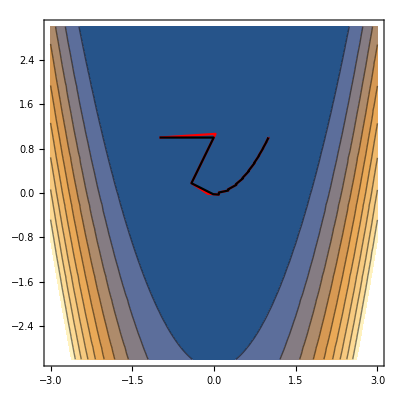

```mathematica
G2 = ListPlot[toch1, PlotStyle->Black,Joined->True];
G3 = ListPlot[toch2, PlotStyle->Red,Joined->True];
Show[G1,G3,G2]
```

```mathematica
(*МНС*)
```

```mathematica
Φ1[a_]=F[x00[[1,1]]-a*GrVToch[x00[[1,1]],x00[[1,2]]][[1]],x00[[1,2]]-a*GrVToch[x00[[1,1]],x00[[1,2]]][[2]]];
```

```mathematica
Trigg1 = {};
toch1 = {x00[[1]]};
```

```mathematica
Do[AppendTo[Trigg1,N[Table[Solve[D[Φ1[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}]][[i]]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}];
```

```mathematica
Trigg1
```

{0.5,0.00125631,0.248744}

```mathematica
α1=Trigg1[[3]];
```

```mathematica
xk = x00[[1]] - α1 * GrVToch[x00[[1,1]],x00[[1,2]]];
```

```mathematica
AppendTo[toch1,xk];
```

```mathematica
k=1;
```

```mathematica
t1=SessionTime[];
```

```mathematica
While[Norm[GrVToch[xk[[1]],xk[[2]]],2]>ϵ,{
Φ1[a_]=F[xk[[1]]-a*GrVToch[xk[[1]],xk[[2]]][[1]],xk[[2]]-a*GrVToch[xk[[1]],xk[[2]]][[2]]];
Trigg1 = {};
Do[If[Element[N[Table[Solve[D[Φ1[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}]][[i]],Reals],AppendTo[Trigg1,N[Table[Solve[D[Φ1[a],a]==0][[i,1,2]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}]][[i]]]],{i,1,Length[Solve[D[Φ1[a],a]==0]]}];
α1=Trigg1[[1]];
For[i=1,i≤ Length[Trigg1],i++,If[Φ1[Trigg1[[i]]]<Φ1[α1],α1=Trigg1[[i]]]];
xk = xk - α1 * GrVToch[xk[[1]],xk[[2]]];
AppendTo[toch1,xk];
k++;

}]
```

```mathematica
Print["Точка xk = ",xk," F(x) = ",F[xk[[1]],xk[[2]]]," шаг α = ",α1," ||∇F(x̄)|| = ",Norm[GrVToch[xk[[1]],xk[[2]]],2]]
```

Точка xk = {0.999001,0.997999} F(x) = 9.99916×10^-7 шаг α = 0.00124937 ||∇F(x̄)|| = 0.000999706

```mathematica
k
```

4339

```mathematica
t2=SessionTime[];
```

```mathematica
AppendTo[Srav,{"Метод наискорейшего спуска",t2-t1,k}];
```

```mathematica
Insert[Grid[Srav],{Dividers->All,Spacings->1.5 {0.4,0.4}},2];
Grid[Srav,Dividers->All]
```

Метод | Время выполнения метода | Количество итераций
Овражный градиентный метод | 1.557439 | 13
Метод наискорейшего спуска | 197.550765 | 4339

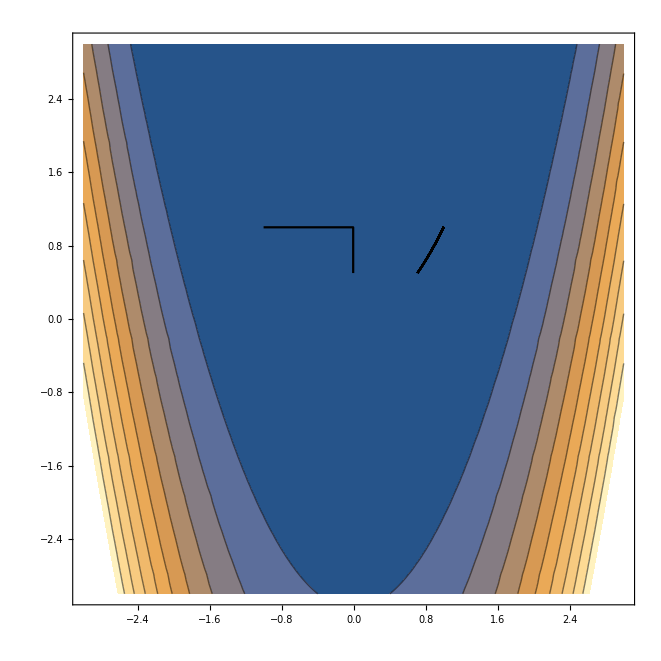

```mathematica
G4 = ListPlot[toch1, PlotStyle->Black,Joined->True];

Show[G1,G4]
```